```mathematica
ClearAll[alpha];
ClearAll[beta];
S = Sqrt[2]*Sin[beta]*(Cos[alpha]*Sin[beta]+Sin[alpha]*Cos[beta]*Cos[theta]);
T = Cos[alpha]*Cos[beta]-Sin[alpha]*Sin[beta]*Cos[theta];
```

{{phi→InterpolatingFunction[{{0., 6.28319}}, <>]}}

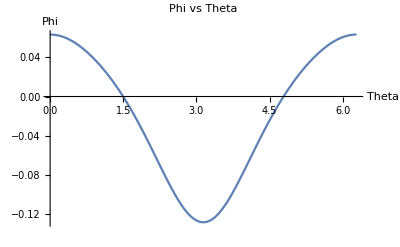

```mathematica
beta=141;
alpha=70.5;
axialMoI=25;
transverseMoI=100;
combinedMoI = axialMoI/transverseMoI;


modelSize = 2*Pi;
sol = NDSolve[{ 
phi'[theta] == (combinedMoI*S)/((T-1)*(1-T+combinedMoI*(1+T))*(1+T)^(1/2)),
phi[0]==0
},{phi},{theta,0,modelSize}]
Plot[phi'[theta]/.sol, {theta,0,modelSize},PlotLabel->"Phi vs Theta",AxesLabel->{"Theta","Phi"}]
```